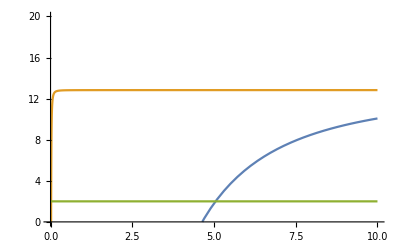

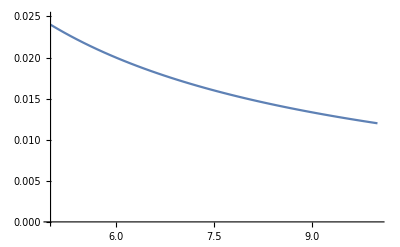

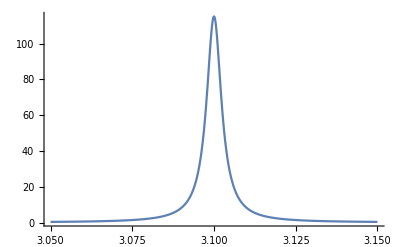

```mathematica
n=1.00044892;
e=Sqrt[p^2+m^2];

Nphe[p_,m_]:=110*130*Sin[ArcCos[1/(n p/Sqrt[p^2+m^2])]]^2;
be[y_]:=y/Sqrt[y^2+m^2];
Plot[{Nphe[y,0.139],Nphe[y,0.0005],2},{y,0.,10.}, PlotRange->{{0,10},{0,20}}]

Plot[.12/x,{x,5,10},PlotRange->{{5,10},{0,0.025}}]

BW[m_,m0_,G_]:=1/Pi*G/2/((m-m0)^2+(G/2)^2);
Plot[BW[m,3.1,0.00553],{m,3.05,3.15},PlotRange->All]
```